# Symmetry Package Demo

Geert van Wordragen

© Copyright 2019 Eindhoven University of Technology, The Netherlands
This software is made available under the terms of the MIT License.

```mathematica
SetDirectory[NotebookDirectory[]];
Needs["Symmetry`","Symmetry.wl"]
```

First, we create a hexagon.

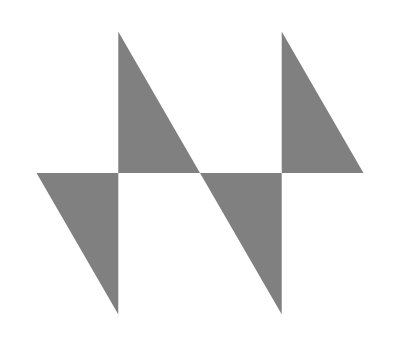

```mathematica
hexagon=CanonicalizePolygon[RegularPolygon[6]];
g={Gray,hexagon};
Graphics[g,ImageSize->Tiny]
```

Next, we can use SymmetryTransformation to find the symmetries of the hexagon, which are given as a TransformationGroup.
The symmetries are generated by a reflection through the y-axis and a rotation over 1/3 π.

```mathematica
symm=SymmetryTransformation[hexagon]
```

TransformationGroup[{Reflection[InfiniteLine[{0,0},{-1,0}]],Rotation[{0,0},π/3]}]

We can visualise the symmetries by using TransformationPrimitive[] on the TransformationGroup.

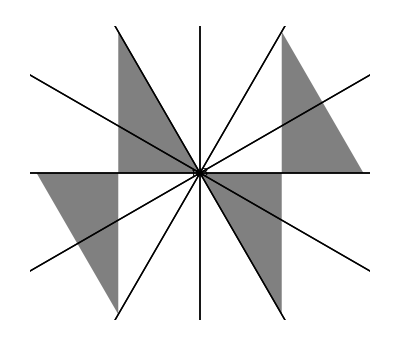

```mathematica
Graphics[{g,TransformationPrimitive[symm]}]
```

Alternatively, we can use SymmetryPermutation to determine the symmetries in the form of a PermutationGroup.
The symmetries are generated by the reflection symmetry that switches vertex 2 with vertex 6 and vertex 3 vertex 5, together with the rotation symmetry that puts each vertex at the position of the one after it.

```mathematica
SymmetryPermutation[hexagon]
```

PermutationGroup[{Cycles[{{2,6},{3,5}}],Cycles[{{1,2,3,4,5,6}}]}]

There are no restrictions on the kind of polygon.

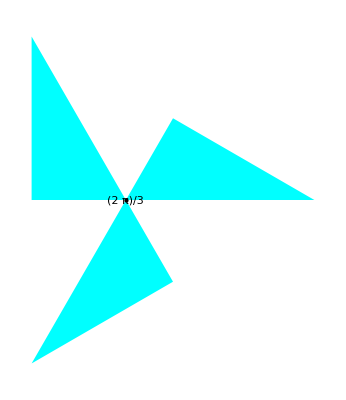

```mathematica
tripleTriangle=Polygon[{{-1/2,-(√3)/2}*2,{1/2,-(√3)/2},{-1/2,(√3)/2}*2,{-1,0},{1,0}*2,{1/2,(√3)/2}}];
Graphics[{Cyan,tripleTriangle,Black,TransformationPrimitive[SymmetryTransformation[tripleTriangle]]}]
```

If the argument has a Point or List head, it is interpreted as a point set.

```mathematica
doubleHexagon=Point[(First@hexagon+1) ~Join~ First@hexagon];
symm=SymmetryTransformation[doubleHexagon];
Graphics[{Red,doubleHexagon,Black,TransformationPrimitive[symm]}]
```

-Graphics-

For more general structures consisting of points and lines, we can use a MeshRegion.

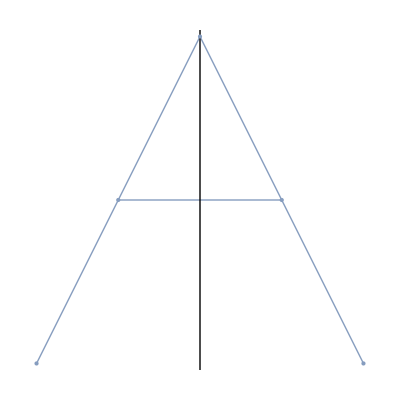

```mathematica
letterA=MeshRegion[{{-1,0},{-.5,1},{0,2},{.5,1},{1,0}},{Line[{1,2,3,4,5}],Line[{2,4}]}];
symm=SymmetryTransformation[letterA];
Show[letterA,Graphics[TransformationPrimitive[symm]]]
```

MeshRegions and BoundaryMeshRegions can be 3-dimensional.

```mathematica
m=PolyhedronData["Cube","BoundaryMeshRegion"];
symm=SymmetryTransformation[m];
Show[m,Graphics3D[{Opacity[.25],TransformationPrimitive[symm]}],PlotRange->{{-1,1},{-1,1},{-1,1}}]
SymmetryPermutation[m]
```

-Graphics3D-

PermutationGroup[{Cycles[{{2,3},{6,7}}],Cycles[{{2,3,5},{4,7,6}}],Cycles[{{2,5},{4,7}}],Cycles[{{2,5,3},{4,6,7}}],Cycles[{{1,2},{3,6},{4,5},{7,8}}],Cycles[{{1,3},{2,4},{5,7},{6,8}}],Cycles[{{1,4},{5,8}}],Cycles[{{1,2},{3,4},{5,6},{7,8}}],Cycles[{{2,3},{6,7}}],Cycles[{{1,2,4,3},{5,6,8,7}}],Cycles[{{1,6},{3,8}}],Cycles[{{1,7,6},{2,3,8}}],Cycles[{{1,3},{2,7},{4,5},{6,8}}],Cycles[{{1,2},{3,4},{5,6},{7,8}}],Cycles[{{2,3},{6,7}}],Cycles[{{1,3},{2,4},{5,7},{6,8}}],Cycles[{{1,4},{5,8}}],Cycles[{{1,2,4,3},{5,6,8,7}}],Cycles[{{1,3},{2,4},{5,7},{6,8}}],Cycles[{{1,7},{2,8}}],Cycles[{{1,5},{2,6},{3,7},{4,8}}],Cycles[{{3,5},{4,6}}],Cycles[{{1,5,7,3},{2,6,8,4}}],Cycles[{{1,2},{3,4},{5,6},{7,8}}],Cycles[{{1,6},{3,8}}],Cycles[{{1,5},{2,6},{3,7},{4,8}}],Cycles[{{2,5},{4,7}}],Cycles[{{1,5,6,2},{3,7,8,4}}],Cycles[{{1,5},{2,7},{3,6},{4,8}}],Cycles[{{1,8},{2,7},{3,4},{5,6}}]}]

Point sets can also be 3 - dimensional

```mathematica
m=Point[{{0,0,1},{0,1,0},{1,0,0}}];
symm=SymmetryTransformation[m];
Graphics3D[{m,TransformationPrimitive[symm]}]
SymmetryPermutation[m]
```

-Graphics3D-

PermutationGroup[{Cycles[{{1,3}}],Cycles[{{1,2}}],Cycles[{{2,3}}],Cycles[{{1,2,3}}],Cycles[{{1,2}}],Cycles[{{1,3}}],Cycles[{{2,3}}],Cycles[{{1,3,2}}]}]

```mathematica
polyhedron="Cuboctahedron";
m=PolyhedronData[polyhedron,"BoundaryMeshRegion"];
symm=SymmetryTransformation[m];
Show[m,Graphics3D[{Opacity[.25],TransformationPrimitive[symm]}],PlotRange->{{-1,1},{-1,1},{-1,1}}]
```

-Graphics3D-

The PermutatioGroup can be used for partitioning of, for example, Hamiltonian cycles.

```mathematica
allCycles=FindHamiltonianCycle[PolyhedronData[polyhedron,"Skeleton"],All];
Print[Length[allCycles]];
```

100

The cuboctahedron has many Hamiltonian cycles, but also many symmetries.

```mathematica
symm=SymmetryPermutation[m];
partitioning={};
remainingCycles=allCycles;
While[remainingCycles≠{},
symmetricCycles=PermutationReplace[First[remainingCycles],symm];
symmetricCycles=Map[RotateLeft[#,First@Position[#,UndirectedEdge[1,_],{1},1]-1]&,symmetricCycles];
symmetricCycles=Intersection[remainingCycles,symmetricCycles];
AppendTo[partitioning,symmetricCycles];
remainingCycles=Complement[remainingCycles,symmetricCycles];
];
Print[Length/@partitioning];
```

{24,24,6,12,4,24,6}

Using the symmetry group we get 7 equivalence classes of symmetric Hamiltonian cycles.